# 7/20/15

## Regular

```mathematica
SetDirectory["C:\\Users\\Justin\\Desktop\\Internship Training 2015\\Regular\\5314"]
```

C:\Users\Justin\Desktop\Internship Training 2015\Regular\5314

```mathematica
Import[fn[[3]]]
```

-Graphics-

```mathematica
x1=Import[fn[[3]],"Data"];
```

```mathematica
Min[x1]
Max[x1]
```

0

552

```mathematica
image=ImageAdjust[Import[fn[[3]]]]
```

-Graphics-

```mathematica
imagedata=ImageData[image,"Bit16"]
```

{«1»}

```mathematica
Min[imagedata]
Max[imagedata]
```

0

65535

```mathematica
slices=ImageAdjust[Import[#]]&/@fn;
Manipulate[slices[[i]],{i,1,27,1}]
```

Import::nffil: File not found during Import.

ImageAdjust::imginv: Expecting an image or graphics instead of $Failed.

Import::nffil: File not found during Import.

ImageAdjust::imginv: Expecting an image or graphics instead of $Failed.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

ImageAdjust::imginv: Expecting an image or graphics instead of $Failed.

General::stop: Further output of ImageAdjust :: imginv will be suppressed during this calculation.

Part::partd: Part specification slices ⟦ 1 ⟧ is longer than depth of object.

```mathematica
slices[[15]]
```

-Graphics-

```mathematica
Manipulate[i,{i,1,Dimensions[slices[[15]]][[1]]}]
```

Part::partw: Part 1 of {} does not exist.

```mathematica
Manipulate[Closing[DeleteSmallComponents[Binarize[slices[[15]],t]],2],{t,0,1,0.001}]
```

Part::partd: Part specification slices ⟦ 15 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slices ⟦ 15 ⟧.

Part::partd: Part specification slices ⟦ 15 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slices ⟦ 15 ⟧.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of Binarize[slices ⟦ 15 ⟧, 0.397].

Closing::arg1: The first argument DeleteSmallComponents[Binarize[slices ⟦ 15 ⟧, 0.397]] is neither a rectangular array nor an image.

Part::partd: Part specification slices ⟦ 15 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slices ⟦ 15 ⟧.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of Binarize[slices ⟦ 15 ⟧, 0.46].

Closing::arg1: The first argument DeleteSmallComponents[Binarize[slices ⟦ 15 ⟧, 0.46]] is neither a rectangular array nor an image.

Part::partd: Part specification slices ⟦ 15 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slices ⟦ 15 ⟧.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of Binarize[slices ⟦ 15 ⟧, 0.46].

Closing::arg1: The first argument DeleteSmallComponents[Binarize[slices ⟦ 15 ⟧, 0.46]] is neither a rectangular array nor an image.

Part::partd: Part specification slices ⟦ 15 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slices ⟦ 15 ⟧.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of Binarize[slices ⟦ 15 ⟧, 0.46].

Closing::arg1: The first argument DeleteSmallComponents[Binarize[slices ⟦ 15 ⟧, 0.46]] is neither a rectangular array nor an image.

```mathematica
test=-Graphics-;
ComponentMeasurements[test,
{"Centroid,PerimeterLength"}]
```

## Irregular

```mathematica
SetDirectory["C:\\Users\\Justin\\Desktop\\Internship Training 2015\\Irregular\\5357"]
fn2=FileNames[];
slicesIrregularRaw=ImageAdjust[Import[#]]&/@fn2;
```

```mathematica
Manipulate[slicesIrregularRaw[[i]],{i,1,198,1}]
```

Part::partd: Part specification slicesIrregularRaw ⟦ 105 ⟧ is longer than depth of object.

Part::partd: Part specification slicesIrregularRaw ⟦ 109 ⟧ is longer than depth of object.

```mathematica
Manipulate[{DeleteSmallComponents[slicesIrregularRaw[[i]]],Colorize@MorphologicalComponents@Binarize[slicesIrregularRaw[[i]],t]},{i,1,198,1},{t,0,1}]
```

Part::partd: Part specification slicesIrregularRaw ⟦ 138 ⟧ is longer than depth of object.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of slicesIrregularRaw ⟦ 138 ⟧.

Part::partd: Part specification slicesIrregularRaw ⟦ 138 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slicesIrregularRaw ⟦ 138 ⟧.

MorphologicalComponents::imginv: Expecting an image or graphics instead of Binarize[slicesIrregularRaw ⟦ 138 ⟧, 0.422].

Colorize::invinput: Expecting an integer matrix or an image instead of MorphologicalComponents[Binarize[slicesIrregularRaw ⟦ 138 ⟧, 0.422]].

```mathematica
DeleteSmallComponents[
Colorize[
ClusteringComponents[
Colorize[
MorphologicalComponents[
Binarize[
Image[
1-ImageData[slicesIrregularRaw[[105]]]
]
,0.762]
]
]
]
]
]
```

-Graphics-

```mathematica
Manipulate[
Colorize[
MorphologicalComponents[
Closing[-Graphics-],t]
],{t,0,1,0.005}]
```

Closing::argr: Closing called with 1 argument; 2 arguments are expected.

MorphologicalComponents::imginv: Expecting an image or graphics instead of ….

Colorize::invinput: Expecting an integer matrix or an image instead of ….

Closing::argr: Closing called with 1 argument; 2 arguments are expected.

MorphologicalComponents::imginv: Expecting an image or graphics instead of ….

Colorize::invinput: Expecting an integer matrix or an image instead of ….

```mathematica
?MorphologicalComponents
```

MorphologicalComponents[image] gives an array in which each pixel of image is replaced by an integer index representing the connected foreground image component in which the pixel lies.
MorphologicalComponents[image,t] treats values above t as foreground.

```mathematica
Colorize[
ClusteringComponents[slicesIrregularRaw[[105]],5]
]
```

-Graphics-

```mathematica
Erosion[Binarize[Image[1-ImageData[slicesIrregularRaw[[105]]]],0.762],0.]
```

-Graphics-

```mathematica
Manipulate[Closing[-Graphics-,t],{t,0,1,0.001}]
```

```mathematica
slicesIrregularRaw
```

```mathematica
?Closing
```

Closing[image,ker] gives the morphological closing of image with respect to the structuring element ker.
Closing[image,r] gives the closing with respect to a range-r square.
Closing[data,…] applies closing to an array of data.

```mathematica
Manipulate[Row@{DeleteSmallComponents[slicesIrregularRaw[[i]]],SelectComponents[Colorize@MorphologicalComponents@Binarize[slicesIrregularRaw[[i]],0.4],"FilledCircularity",6]},{i,1,198,1}]
```

Part::partd: Part specification slicesIrregularRaw ⟦ 149 ⟧ is longer than depth of object.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of slicesIrregularRaw ⟦ 149 ⟧.

Part::partd: Part specification slicesIrregularRaw ⟦ 149 ⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of slicesIrregularRaw ⟦ 149 ⟧.

MorphologicalComponents::imginv: Expecting an image or graphics instead of Binarize[slicesIrregularRaw ⟦ 149 ⟧, 0.4].

Colorize::invinput: Expecting an integer matrix or an image instead of MorphologicalComponents[Binarize[slicesIrregularRaw ⟦ 149 ⟧, 0.4]].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of Colorize[MorphologicalComponents[Binarize[slicesIrregularRaw ⟦ 149 ⟧, 0.4]]].

```mathematica
Select[SortBy[Tally[Flatten[MorphologicalComponents[-Graphics-]]],#[[2]]&],
#==SortBy[Tally[Flatten[MorphologicalComponents[-Graphics-]]],#[[2]]&][[-2]]&]
```

{{2,477}}

```mathematica
Select[
MorphologicalComponents[-Graphics-],
SortBy[Tally[Flatten[MorphologicalComponents[-Graphics-]]],#[[2]]&]==SortBy[Tally[Flatten[MorphologicalComponents[-Graphics-]]],#[[2]]&][[-2]]&
]
```

Part::partw: Part -2 of {{1, 570}} does not exist.

$Aborted

```mathematica
SortBy[Tally[Flatten[MorphologicalComponents[-Graphics-]]],#[[2]]&][[-2]]
```

{2,477}

```mathematica
slice=slices[[15]]
```

-Graphics-

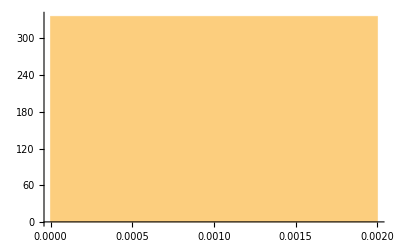

```mathematica
Histogram[ImageData[slice][[10]]]
```

ListLinePlot::lpn: is not a list of numbers or pairs of numbers.

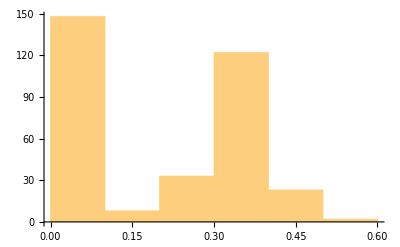
ListLinePlot[-Graphics-]

```mathematica
ListLinePlot@Histogram[ImageData[slice][[161]]]
```

```mathematica
ListLinePlot[slice[[-161]],PlotRange->{0,height}]
```

Part::partd: Part specification … is longer than depth of object.

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.

ListLinePlot[(-Graphics-)⟦-161⟧,PlotRange→{0,336}]

```mathematica
ListLinePlot[ImageData@slice[[-1]],PlotRange->{0,height}]
```

Part::partd: Part specification … is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of ….

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.

ListLinePlot[ImageData[(-Graphics-)⟦-1⟧],PlotRange→{0,336}]

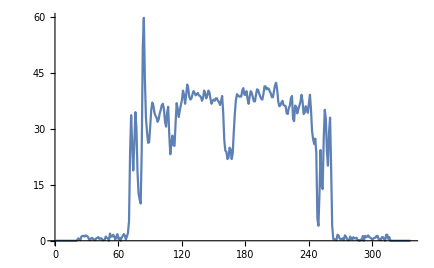

```mathematica
ListLinePlot[100*ImageData[slice][[161]]]
```

```mathematica
Line@Map[ImageData[slice][[161]][[#]]]&/@height
```

336

```mathematica
{width,height}=ImageDimensions[slice];
Manipulate[Show[slice,Graphics[{Yellow,Line[{{0,i},{width,i}}]}],ListLinePlot[100 slice[[-i]]+i,PlotRange->{1,336},PlotStyle->Yellow]],{i,1,height,1}]
```

Part::pkspec1: The expression -i cannot be used as a part specification.

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Part::pkspec1: The expression -i cannot be used as a part specification.

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Part::pkspec1: The expression -i cannot be used as a part specification.

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression -i cannot be used as a part specification.

ListLinePlot::lpn: i + 100.\ slice ⟦ -i ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in slice, GraphicsBox[List[RGBColor[1, 1, 0], LineBox[List[List[0, i], List[width, i]]]]], ListLinePlot[i + 100 slice ⟦ -i ⟧, PlotRange → {1, 336}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[1, 1, 0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.6666666666666666`, 0.6666666666666666`, 0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Part::pkspec1: The expression -i cannot be used as a part specification.

ListLinePlot::lpn: i + 100.\ slice ⟦ -i ⟧ is not a list of numbers or pairs of numbers.